## Equations

```mathematica
exponential = A0 Exp[r*t]
```

A0 ⅇ^(r t)

```mathematica
gaussian=A/(σ*Sqrt[2 π])*Exp[-.5*((t-μ)/σ)^2]
```

(A ⅇ^(-(0.5 (t-μ)^2)/σ^2))/(√(2 π) σ)

```mathematica
gaussian2=A*Exp[-(t-μ)^2/(2 σ^2)]
```

A ⅇ^(-(t-μ)^2/(2 σ^2))

```mathematica
logistic = L/(1+Exp[-k*(t-t0)])
```

L/(1+ⅇ^(-k (t-t0)))

## Data

```mathematica
rawDataAll = Import["C:\\Users\\benho\\OneDrive - Bridgewater State University\\Spring 20\\PHYS 403 - Math Physics\\COVID project\\_Presentation\\Sunday_5-3-20\\COVID_data_20200506.csv"];
TableForm[rawDataAll]
```

| Belgium | Eps | New | Brazil | Eps | New | Canada | Eps | New | US | Eps | New | Connecticut | Eps | New | Massachusetts | Eps | New | New York | Eps | New | Texas | Eps | New
1/22/20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/23/20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/24/20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/25/20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/26/20 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 5. | 2.5 | 3. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/27/20 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 5. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/28/20 | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 2. | 1. | 5. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/29/20 | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 1. | 0. | 5. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/30/20 | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 1. | 0. | 5. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1/31/20 | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 2. | 2. | 7. | 1.4 | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/1/20 | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 1. | 0. | 8. | 1.14286 | 1. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
2/2/20 | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 1. | 0. | 8. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/3/20 | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 1. | 0. | 11. | 1.375 | 3. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/4/20 | 1. | 0. | 1. | 0. | 0. | 0. | 4. | 1. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/5/20 | 1. | 1. | 0. | 0. | 0. | 0. | 5. | 1.25 | 1. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/6/20 | 1. | 1. | 0. | 0. | 0. | 0. | 5. | 1. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/7/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1.4 | 2. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/8/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/9/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/10/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/11/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 12. | 1.09091 | 1. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/12/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 12. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/13/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 13. | 1.08333 | 1. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/14/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/15/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/16/20 | 1. | 1. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/17/20 | 1. | 1. | 0. | 0. | 0. | 0. | 8. | 1.14286 | 1. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/18/20 | 1. | 1. | 0. | 0. | 0. | 0. | 8. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/19/20 | 1. | 1. | 0. | 0. | 0. | 0. | 8. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/20/20 | 1. | 1. | 0. | 0. | 0. | 0. | 8. | 1. | 0. | 13. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/21/20 | 1. | 1. | 0. | 0. | 0. | 0. | 9. | 1.125 | 1. | 15. | 1.15385 | 2. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/22/20 | 1. | 1. | 0. | 0. | 0. | 0. | 9. | 1. | 0. | 15. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/23/20 | 1. | 1. | 0. | 0. | 0. | 0. | 9. | 1. | 0. | 15. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/24/20 | 1. | 1. | 0. | 0. | 0. | 0. | 10. | 1.11111 | 1. | 51. | 3.4 | 36. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/25/20 | 1. | 1. | 0. | 0. | 0. | 0. | 11. | 1.1 | 1. | 51. | 1. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/26/20 | 1. | 1. | 0. | 1. | 0. | 1. | 11. | 1. | 0. | 57. | 1.11765 | 6. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/27/20 | 1. | 1. | 0. | 1. | 1. | 0. | 13. | 1.18182 | 2. | 58. | 1.01754 | 1. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/28/20 | 1. | 1. | 0. | 1. | 1. | 0. | 14. | 1.07692 | 1. | 60. | 1.03448 | 2. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2/29/20 | 1. | 1. | 0. | 2. | 2. | 1. | 20. | 1.42857 | 6. | 68. | 1.13333 | 8. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3/1/20 | 2. | 2. | 1. | 2. | 1. | 0. | 24. | 1.2 | 4. | 74. | 1.08824 | 6. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3/2/20 | 8. | 4. | 6. | 2. | 1. | 0. | 27. | 1.125 | 3. | 98. | 1.32432 | 24. | 0. | 0. | 0. | 1. | 1. | 0. | 1. | 0. | 1. | 0. | 0. | 0.
3/3/20 | 13. | 1.625 | 5. | 2. | 1. | 0. | 30. | 1.11111 | 3. | 118. | 1.20408 | 20. | 0. | 0. | 0. | 2. | 2. | 1. | 2. | 2. | 1. | 0. | 0. | 0.
3/4/20 | 23. | 1.76923 | 10. | 4. | 2. | 2. | 33. | 1.1 | 3. | 149. | 1.26271 | 31. | 0. | 0. | 0. | 2. | 1. | 0. | 11. | 5.5 | 9. | 0. | 0. | 0.
3/5/20 | 50. | 2.17391 | 27. | 4. | 1. | 0. | 37. | 1.12121 | 4. | 217. | 1.45638 | 68. | 0. | 0. | 0. | 2. | 1. | 0. | 23. | 2.09091 | 12. | 3. | 0. | 3.
3/6/20 | 109. | 2.18 | 59. | 13. | 3.25 | 9. | 49. | 1.32432 | 12. | 262. | 1.20737 | 45. | 0. | 0. | 0. | 6. | 3. | 4. | 31. | 1.34783 | 8. | 4. | 1.33333 | 1.
3/7/20 | 169. | 1.55046 | 60. | 13. | 1. | 0. | 54. | 1.10204 | 5. | 402. | 1.53435 | 140. | 0. | 0. | 0. | 6. | 1. | 0. | 76. | 2.45161 | 45. | 8. | 2. | 4.
3/8/20 | 200. | 1.18343 | 31. | 20. | 1.53846 | 7. | 64. | 1.18519 | 10. | 518. | 1.28856 | 116. | 0. | 0. | 0. | 22. | 3.66667 | 16. | 106. | 1.39474 | 30. | 11. | 1.375 | 3.
3/9/20 | 239. | 1.195 | 39. | 25. | 1.25 | 5. | 77. | 1.20313 | 13. | 583. | 1.12548 | 65. | 0. | 0. | 0. | 22. | 1. | 0. | 142. | 1.33962 | 36. | 13. | 1.18182 | 2.
3/10/20 | 267. | 1.11715 | 28. | 31. | 1.24 | 6. | 79. | 1.02597 | 2. | 959. | 1.64494 | 376. | 1. | 0. | 1. | 41. | 1.86364 | 19. | 150. | 1.05634 | 8. | 16. | 1.23077 | 3.
3/11/20 | 314. | 1.17603 | 47. | 38. | 1.22581 | 7. | 108. | 1.36709 | 29. | 1281. | 1.33577 | 322. | 3. | 3. | 2. | 92. | 2.2439 | 51. | 220. | 1.46667 | 70. | 21. | 1.3125 | 5.
3/12/20 | 314. | 1. | 0. | 52. | 1.36842 | 14. | 117. | 1.08333 | 9. | 1663. | 1.2982 | 382. | 5. | 1.66667 | 2. | 107. | 1.16304 | 15. | 327. | 1.48636 | 107. | 27. | 1.28571 | 6.
3/13/20 | 559. | 1.78025 | 245. | 151. | 2.90385 | 99. | 193. | 1.64957 | 76. | 2179. | 1.31028 | 516. | 11. | 2.2 | 6. | 123. | 1.14953 | 16. | 421. | 1.28746 | 94. | 44. | 1.62963 | 17.
3/14/20 | 689. | 1.23256 | 130. | 151. | 1. | 0. | 198. | 1.02591 | 5. | 2727. | 1.25149 | 548. | 23. | 2.09091 | 12. | 138. | 1.12195 | 15. | 613. | 1.45606 | 192. | 60. | 1.36364 | 16.
3/15/20 | 886. | 1.28592 | 197. | 162. | 1.07285 | 11. | 252. | 1.27273 | 54. | 3499. | 1.28309 | 772. | 24. | 1.04348 | 1. | 138. | 1. | 0. | 615. | 1.00326 | 2. | 63. | 1.05 | 3.
3/16/20 | 1058. | 1.19413 | 172. | 200. | 1.23457 | 38. | 415. | 1.64683 | 163. | 4632. | 1.32381 | 1133. | 41. | 1.70833 | 17. | 187. | 1.35507 | 49. | 967. | 1.57236 | 352. | 85. | 1.34921 | 22.
3/17/20 | 1243. | 1.17486 | 185. | 321. | 1.605 | 121. | 478. | 1.15181 | 63. | 6421. | 1.38623 | 1789. | 68. | 1.65854 | 27. | 217. | 1.16043 | 30. | 1578. | 1.63185 | 611. | 110. | 1.29412 | 25.
3/18/20 | 1486. | 1.19549 | 243. | 372. | 1.15888 | 51. | 657. | 1.37448 | 179. | 7783. | 1.21212 | 1362. | 96. | 1.41176 | 28. | 252. | 1.16129 | 35. | 3038. | 1.92522 | 1460. | 196. | 1.78182 | 86.
3/19/20 | 1795. | 1.20794 | 309. | 621. | 1.66935 | 249. | 800. | 1.21766 | 143. | 13747. | 1.76629 | 5964. | 159. | 1.65625 | 63. | 328. | 1.30159 | 76. | 5704. | 1.87755 | 2666. | 306. | 1.56122 | 110.
3/20/20 | 2257. | 1.25738 | 462. | 793. | 1.27697 | 172. | 943. | 1.17875 | 143. | 19273. | 1.40198 | 5526. | 194. | 1.22013 | 35. | 413. | 1.25915 | 85. | 8403. | 1.47318 | 2699. | 429. | 1.40196 | 123.
3/21/20 | 2815. | 1.24723 | 558. | 1021. | 1.28752 | 228. | 1277. | 1.35419 | 334. | 25600. | 1.32828 | 6327. | 194. | 1. | 0. | 523. | 1.26634 | 110. | 11727. | 1.39557 | 3324. | 582. | 1.35664 | 153.
3/22/20 | 3401. | 1.20817 | 586. | 1546. | 1.5142 | 525. | 1469. | 1.15035 | 192. | 33276. | 1.29984 | 7676. | 327. | 1.68557 | 133. | 640. | 1.22371 | 117. | 15800. | 1.34732 | 4073. | 643. | 1.10481 | 61.
3/23/20 | 3743. | 1.10056 | 342. | 1924. | 1.2445 | 378. | 2088. | 1.42138 | 619. | 43843. | 1.31756 | 10567. | 415. | 1.26911 | 88. | 777. | 1.21406 | 137. | 20884. | 1.32177 | 5084. | 758. | 1.17885 | 115.
3/24/20 | 4269. | 1.14053 | 526. | 2247. | 1.16788 | 323. | 2790. | 1.33621 | 702. | 53736. | 1.22565 | 9893. | 618. | 1.48916 | 203. | 1159. | 1.49163 | 382. | 25681. | 1.2297 | 4797. | 955. | 1.25989 | 197.
3/25/20 | 4937. | 1.15648 | 668. | 2554. | 1.13663 | 307. | 3251. | 1.16523 | 461. | 65778. | 1.2241 | 12042. | 875. | 1.41586 | 257. | 1838. | 1.58585 | 679. | 30841. | 1.20093 | 5160. | 1229. | 1.28691 | 274.
3/26/20 | 6235. | 1.26291 | 1298. | 2985. | 1.16875 | 431. | 4042. | 1.24331 | 791. | 83836. | 1.27453 | 18058. | 1012. | 1.15657 | 137. | 2417. | 1.31502 | 579. | 37877. | 1.22814 | 7036. | 1563. | 1.27177 | 334.
3/27/20 | 7284. | 1.16824 | 1049. | 3417. | 1.14472 | 432. | 4682. | 1.15834 | 640. | 101657. | 1.21257 | 17821. | 1291. | 1.27569 | 279. | 3240. | 1.3405 | 823. | 44876. | 1.18478 | 6999. | 1937. | 1.23928 | 374.
3/28/20 | 9134. | 1.25398 | 1850. | 3904. | 1.14252 | 487. | 5576. | 1.19094 | 894. | 121465. | 1.19485 | 19808. | 1524. | 1.18048 | 233. | 4257. | 1.31389 | 1017. | 52410. | 1.16788 | 7534. | 2455. | 1.26742 | 518.
3/29/20 | 10836. | 1.18634 | 1702. | 4256. | 1.09016 | 352. | 6280. | 1.12626 | 704. | 140909. | 1.16008 | 19444. | 1993. | 1.30774 | 469. | 4955. | 1.16397 | 698. | 59648. | 1.1381 | 7238. | 2792. | 1.13727 | 337.
3/30/20 | 11899. | 1.0981 | 1063. | 4579. | 1.07589 | 323. | 7398. | 1.17803 | 1118. | 161831. | 1.14848 | 20922. | 2571. | 1.29002 | 578. | 5752. | 1.16085 | 797. | 66663. | 1.11761 | 7015. | 3147. | 1.12715 | 355.
3/31/20 | 12775. | 1.07362 | 876. | 5717. | 1.24853 | 1138. | 8527. | 1.15261 | 1129. | 188172. | 1.16277 | 26341. | 3128. | 1.21665 | 557. | 6620. | 1.1509 | 868. | 75833. | 1.13756 | 9170. | 3809. | 1.21036 | 662.
4/1/20 | 13964. | 1.09307 | 1189. | 6836. | 1.19573 | 1119. | 9560. | 1.12114 | 1033. | 213242. | 1.13323 | 25070. | 3557. | 1.13715 | 429. | 7738. | 1.16888 | 1118. | 83948. | 1.10701 | 8115. | 4355. | 1.14334 | 546.
4/2/20 | 15348. | 1.09911 | 1384. | 8044. | 1.17671 | 1208. | 11284. | 1.18033 | 1724. | 243622. | 1.14247 | 30380. | 3824. | 1.07506 | 267. | 8966. | 1.1587 | 1228. | 92506. | 1.10194 | 8558. | 5069. | 1.16395 | 714.
4/3/20 | 16770. | 1.09265 | 1422. | 9056. | 1.12581 | 1012. | 12437. | 1.10218 | 1153. | 275367. | 1.1303 | 31745. | 4914. | 1.28504 | 1090. | 10402. | 1.16016 | 1436. | 102987. | 1.1133 | 10481. | 5734. | 1.13119 | 665.
4/4/20 | 18431. | 1.09905 | 1661. | 10360. | 1.14399 | 1304. | 12978. | 1.0435 | 541. | 308650. | 1.12087 | 33283. | 5276. | 1.07367 | 362. | 11736. | 1.12824 | 1334. | 113833. | 1.10531 | 10846. | 6567. | 1.14527 | 833.
4/5/20 | 19691. | 1.06836 | 1260. | 11130. | 1.07432 | 770. | 15756. | 1.21405 | 2778. | 336802. | 1.09121 | 28152. | 5675. | 1.07563 | 399. | 12500. | 1.0651 | 764. | 123160. | 1.08194 | 9327. | 7209. | 1.09776 | 642.
4/6/20 | 20814. | 1.05703 | 1123. | 12161. | 1.09263 | 1031. | 16563. | 1.05122 | 807. | 366317. | 1.08763 | 29515. | 6906. | 1.21692 | 1231. | 13837. | 1.10696 | 1337. | 131815. | 1.07027 | 8655. | 8043. | 1.11569 | 834.
4/7/20 | 22194. | 1.0663 | 1380. | 14034. | 1.15402 | 1873. | 17872. | 1.07903 | 1309. | 397121. | 1.08409 | 30804. | 7781. | 1.1267 | 875. | 15202. | 1.09865 | 1365. | 139875. | 1.06115 | 8060. | 8925. | 1.10966 | 882.
4/8/20 | 23403. | 1.05447 | 1209. | 16170. | 1.1522 | 2136. | 19141. | 1.071 | 1269. | 428654. | 1.0794 | 31533. | 7781. | 1. | 0. | 16790. | 1.10446 | 1588. | 151061. | 1.07997 | 11186. | 9777. | 1.09546 | 852.
4/9/20 | 24983. | 1.06751 | 1580. | 18092. | 1.11886 | 1922. | 20654. | 1.07904 | 1513. | 462780. | 1.07961 | 34126. | 9784. | 1.25742 | 2003. | 18941. | 1.12811 | 2151. | 161779. | 1.07095 | 10718. | 11208. | 1.14636 | 1431.
4/10/20 | 26667. | 1.06741 | 1684. | 19638. | 1.08545 | 1546. | 22059. | 1.06803 | 1405. | 496535. | 1.07294 | 33755. | 10538. | 1.07706 | 754. | 20974. | 1.10733 | 2033. | 172348. | 1.06533 | 10569. | 12105. | 1.08003 | 897.
4/11/20 | 28018. | 1.05066 | 1351. | 20727. | 1.05545 | 1089. | 23316. | 1.05698 | 1257. | 526396. | 1.06014 | 29861. | 11510. | 1.09224 | 972. | 22860. | 1.08992 | 1886. | 181026. | 1.05035 | 8678. | 13023. | 1.07584 | 918.
4/12/20 | 29647. | 1.05814 | 1629. | 22192. | 1.07068 | 1465. | 24299. | 1.04216 | 983. | 555313. | 1.05493 | 28917. | 12035. | 1.04561 | 525. | 25475. | 1.11439 | 2615. | 189033. | 1.04423 | 8007. | 13677. | 1.05022 | 654.
4/13/20 | 30589. | 1.03177 | 942. | 23430. | 1.05579 | 1238. | 25680. | 1.05683 | 1381. | 580619. | 1.04557 | 25306. | 13381. | 1.11184 | 1346. | 26867. | 1.05464 | 1392. | 195749. | 1.03553 | 6716. | 14275. | 1.04372 | 598.
4/14/20 | 31119. | 1.01733 | 530. | 25262. | 1.07819 | 1832. | 27035. | 1.05276 | 1355. | 607670. | 1.04659 | 27051. | 13989. | 1.04544 | 608. | 28164. | 1.04827 | 1297. | 203020. | 1.03714 | 7271. | 15006. | 1.05121 | 731.
4/15/20 | 33573. | 1.07886 | 2454. | 28320. | 1.12105 | 3058. | 28209. | 1.04343 | 1174. | 636350. | 1.0472 | 28680. | 14755. | 1.05476 | 766. | 29918. | 1.06228 | 1754. | 214454. | 1.05632 | 11434. | 15907. | 1.06004 | 901.
4/16/20 | 34809. | 1.03682 | 1236. | 30425. | 1.07433 | 2105. | 30809. | 1.09217 | 2600. | 667592. | 1.0491 | 31242. | 15884. | 1.07652 | 1129. | 32181. | 1.07564 | 2263. | 223691. | 1.04307 | 9237. | 16876. | 1.06092 | 969.
4/17/20 | 36138. | 1.03818 | 1329. | 33682. | 1.10705 | 3257. | 32814. | 1.06508 | 2005. | 699706. | 1.0481 | 32114. | 16809. | 1.05823 | 925. | 34402. | 1.06902 | 2221. | 230597. | 1.03087 | 6906. | 17849. | 1.05766 | 973.
4/18/20 | 37183. | 1.02892 | 1045. | 36658. | 1.08836 | 2976. | 34356. | 1.04699 | 1542. | 732197. | 1.04644 | 32491. | 17550. | 1.04408 | 741. | 36372. | 1.05726 | 1970. | 237474. | 1.02982 | 6877. | 18704. | 1.0479 | 855.
4/19/20 | 38496. | 1.03531 | 1313. | 38654. | 1.05445 | 1996. | 35633. | 1.03717 | 1277. | 758809. | 1.03635 | 26612. | 17962. | 1.02348 | 412. | 38077. | 1.04688 | 1705. | 243382. | 1.02488 | 5908. | 19260. | 1.02973 | 556.
4/20/20 | 39983. | 1.03863 | 1487. | 40743. | 1.05404 | 2089. | 37658. | 1.05683 | 2025. | 784326. | 1.03363 | 25517. | 19815. | 1.10316 | 1853. | 38077. | 1. | 0. | 248416. | 1.02068 | 5034. | 19751. | 1.02549 | 491.
4/21/20 | 40956. | 1.02434 | 973. | 43079. | 1.05734 | 2336. | 39402. | 1.04631 | 1744. | 811865. | 1.03511 | 27539. | 20360. | 1.0275 | 545. | 41199. | 1.08199 | 3122. | 253519. | 1.02054 | 5103. | 20574. | 1.04167 | 823.
4/22/20 | 41889. | 1.02278 | 933. | 45757. | 1.06216 | 2678. | 41663. | 1.05738 | 2261. | 840351. | 1.03509 | 28486. | 22469. | 1.10359 | 2109. | 42944. | 1.04236 | 1745. | 258222. | 1.01855 | 4703. | 21321. | 1.03631 | 747.
4/23/20 | 42797. | 1.02168 | 908. | 50036. | 1.09352 | 4279. | 43299. | 1.03927 | 1636. | 869170. | 1.03429 | 28819. | 23100. | 1.02808 | 631. | 46023. | 1.0717 | 3079. | 263460. | 1.02028 | 5238. | 22650. | 1.06233 | 1329.
4/24/20 | 44293. | 1.03496 | 1496. | 54043. | 1.08008 | 4007. | 44919. | 1.03741 | 1620. | 905358. | 1.04164 | 36188. | 23936. | 1.03619 | 836. | 50969. | 1.10747 | 4946. | 271590. | 1.03086 | 8130. | 23642. | 1.0438 | 992.
4/25/20 | 45325. | 1.0233 | 1032. | 59324. | 1.09772 | 5281. | 46371. | 1.03232 | 1452. | 938154. | 1.03622 | 32796. | 24583. | 1.02703 | 647. | 53348. | 1.04668 | 2379. | 282143. | 1.03886 | 10553. | 24153. | 1.02161 | 511.
4/26/20 | 46134. | 1.01785 | 809. | 63100. | 1.06365 | 3776. | 48033. | 1.03584 | 1662. | 965785. | 1.02945 | 27631. | 25269. | 1.02791 | 686. | 54938. | 1.0298 | 1590. | 288045. | 1.02092 | 5902. | 24967. | 1.0337 | 814.
4/27/20 | 46687. | 1.01199 | 553. | 67446. | 1.06887 | 4346. | 49616. | 1.03296 | 1583. | 988197. | 1.02321 | 22412. | 25997. | 1.02881 | 728. | 56462. | 1.02774 | 1524. | 291996. | 1.01372 | 3951. | 25321. | 1.01418 | 354.
4/28/20 | 47334. | 1.01386 | 647. | 73235. | 1.08583 | 5789. | 51150. | 1.03092 | 1534. | 1.01258×10^6 | 1.02468 | 24385. | 26312. | 1.01212 | 315. | 58302. | 1.03259 | 1840. | 295106. | 1.01065 | 3110. | 26357. | 1.04091 | 1036.
4/29/20 | 47859. | 1.01109 | 525. | 79685. | 1.08807 | 6450. | 52865. | 1.03353 | 1715. | 1.03991×10^6 | 1.02699 | 27327. | 26767. | 1.01729 | 455. | 60265. | 1.03367 | 1963. | 299691. | 1.01554 | 4585. | 27257. | 1.03415 | 900.
4/30/20 | 48519. | 1.01379 | 660. | 87187. | 1.09415 | 7502. | 54457. | 1.03011 | 1592. | 1.06942×10^6 | 1.02838 | 29515. | 27700. | 1.03486 | 933. | 62205. | 1.03219 | 1940. | 304372. | 1.01562 | 4681. | 28727. | 1.05393 | 1470.
5/1/20 | 49032. | 1.01057 | 513. | 92202. | 1.05752 | 5015. | 56343. | 1.03463 | 1886. | 1.10346×10^6 | 1.03183 | 34037. | 28764. | 1.03841 | 1064. | 64311. | 1.03386 | 2106. | 308314. | 1.01295 | 3942. | 29692. | 1.03359 | 965.
5/2/20 | 49517. | 1.00989 | 485. | 97100. | 1.05312 | 4898. | 57926. | 1.0281 | 1583. | 1.13254×10^6 | 1.02635 | 29078. | 29287. | 1.01818 | 523. | 66263. | 1.03035 | 1952. | 312977. | 1.01512 | 4663. | 30917. | 1.04126 | 1225.
5/3/20 | 49906. | 1.00786 | 389. | 101826. | 1.04867 | 4726. | 60504. | 1.04451 | 2578. | 1.15804×10^6 | 1.02252 | 25501. | 29287. | 1. | 0. | 68087. | 1.02753 | 1824. | 316415. | 1.01098 | 3438. | 31998. | 1.03496 | 1081.
5/4/20 | 50267. | 1.00723 | 361. | 108620. | 1.06672 | 6794. | 61957. | 1.02401 | 1453. | 1.18038×10^6 | 1.01929 | 22335. | 29973. | 1.02342 | 686. | 69087. | 1.01469 | 1000. | 318953. | 1.00802 | 2538. | 32783. | 1.02453 | 785.
5/5/20 | 50509. | 1.00481 | 242. | 115455. | 1.06293 | 6835. | 63215. | 1.0203 | 1258. | 1.20435×10^6 | 1.02031 | 23976. | 30621. | 1.02162 | 648. | 70271. | 1.01714 | 1184. | 321192. | 1.00702 | 2239. | 33912. | 1.03444 | 1129.

## Graphs

#### Raw data

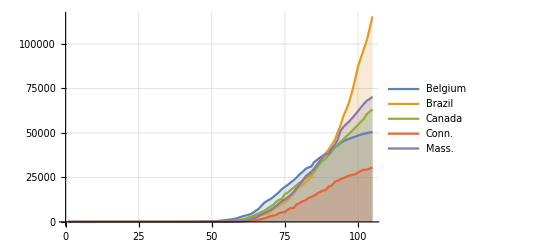

```mathematica
ListLinePlot[{rawDataAll[[2;;,2]],rawDataAll[[2;;,5]],rawDataAll[[2;;,8]],rawDataAll[[2;;,14]],rawDataAll[[2;;,17]]},Filling->Axis,PlotRange->All,PlotLegends->Placed[{"Belgium","Brazil","Canada","Conn.","Mass."},{Left,Center}],GridLines->Automatic]
```

#### Exponential

```mathematica
expBelgium = NonlinearModelFit[rawDataAll[[2;;,2]],exponential,{{A0,250},{r,.07}},t];
ebe=expBelgium["ParameterTableEntries"];
expBrazil = NonlinearModelFit[rawDataAll[[2;;,5]],exponential,{{A0,20},{r,.08}},t];
ebr=expBrazil["ParameterTableEntries"];
expCanada = NonlinearModelFit[rawDataAll[[2;;,8]],exponential,{{A0,100},{r,.06}},t];
eca=expCanada["ParameterTableEntries"];
expConn = NonlinearModelFit[rawDataAll[[2;;,14]],exponential,{{A0,20},{r,.07}},t];ect=expConn["ParameterTableEntries"];
expMass= NonlinearModelFit[rawDataAll[[2;;,17]],exponential,{{A0,40},{r,.07}},t];
ema=expMass["ParameterTableEntries"]
```

{{187.857,30.6433,6.13045,1.63275×10^-8},{0.0579318,0.00167745,34.5357,1.90091×10^-58}}

```mathematica
Grid[{{"Exponential Parameters",SpanFromLeft},{"Place","A0","r"},{"Belgium",ebe[[1]][[1]],ebe[[2]][[1]]},{"Brazil",ebr[[1]][[1]],ebr[[2]][[1]]},{"Canada",eca[[1]][[1]],eca[[2]][[1]]},{"Conn.",ect[[1]][[1]],ect[[2]][[1]]},{"Mass.",ema[[1]][[1]],ema[[2]][[1]]}},Frame->All]
```

Exponential Parameters |  | 
Place | A0 | r
Belgium | 627.088 | 0.043931
Brazil | 44.7238 | 0.0752866
Canada | 265.824 | 0.0533841
Conn. | 115.923 | 0.0548523
Mass. | 187.857 | 0.0579318

```mathematica
First[%17]
```

{{Exponential Parameters,},{Place,A0,r},{Belgium,627.088,0.043931},{Brazil,44.7238,0.0752866},{Canada,265.824,0.0533841},{Conn.,115.923,0.0548523},{Mass.,187.857,0.0579318}}

```mathematica
First[%17]
```

{{Exponential Parameters,},{Place,A0,r},{Belgium,627.088,0.043931},{Brazil,44.7238,0.0752866},{Canada,265.824,0.0533841},{Conn.,115.923,0.0548523},{Mass.,187.857,0.0579318}}

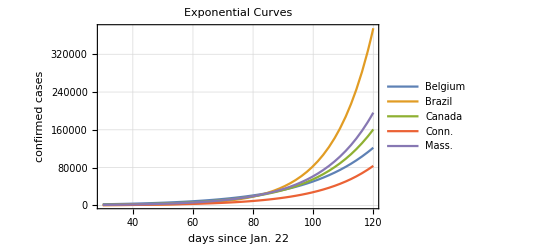

```mathematica
Plot[{expBelgium[t],expBrazil[t],expCanada[t],expConn[t],expMass[t]},{t,30,120},GridLines->Automatic,PlotRange->All,PlotLabel->Style["Exponential Curves",Bold,Black],PlotLegends->Placed[{"Belgium","Brazil","Canada","Conn.","Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

### Logistic

```mathematica
logBelgium=NonlinearModelFit[rawDataAll[[2;;,2]],logistic,{{L,48215},{k,.14},{t0,77}},t];
lbe=logBelgium["ParameterTableEntries"];
logBrazil=NonlinearModelFit[rawDataAll[[2;;,5]],logistic,{{L,200000},{k,.09},{t0,106}},t];
lbr=logBrazil["ParameterTableEntries"];
logCanada=NonlinearModelFit[rawDataAll[[2;;,8]],logistic,{{L,54051},{k,.13},{t0,82}},t];
lca=logCanada["ParameterTableEntries"];
logConn=NonlinearModelFit[rawDataAll[[2;;,14]],logistic,{{L,28927},{k,.15},{t0,84}},t];
lct=logConn["ParameterTableEntries"];
logMass=NonlinearModelFit[rawDataAll[[2;;,17]],logistic,{{L,26121},{k,.15},{t0,81}},t];
lma=logMass["ParameterTableEntries"]
```

{{81210.7,1274.07,63.7413,5.49967×10^-84},{0.118297,0.00232143,50.9588,2.25791×10^-74},{89.8402,0.34225,262.498,3.56292×10^-146}}

```mathematica
Grid[{{"Logistic Parameters",SpanFromLeft},{"Place","L","k","t0"},{"Belgium",lbe[[1]][[1]],lbe[[2]][[1]],lbe[[3]][[1]]},{"Brazil",lbr[[1]][[1]],lbr[[2]][[1]],lbr[[3]][[1]]},{"Canada",lca[[1]][[1]],lca[[2]][[1]],lca[[3]][[1]]},{"Conn.",lct[[1]][[1]],lct[[2]][[1]],lct[[3]][[1]]},{"Mass.",lma[[1]][[1]],lma[[2]][[1]],lma[[3]][[1]]}},Frame->All]
```

Logistic Parameters |  |  | 
Place | L | k | t0
Belgium | 51960.7 | 0.125532 | 79.8313
Brazil | 265733. | 0.0957283 | 107.851
Canada | 71583. | 0.107236 | 88.6515
Conn. | 32174.1 | 0.136185 | 86.1907
Mass. | 81210.7 | 0.118297 | 89.8402

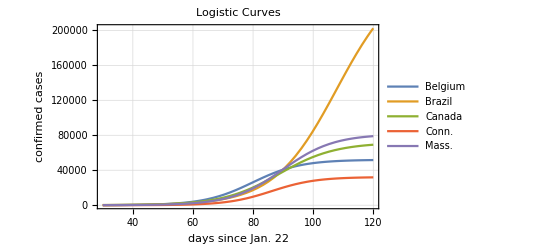

```mathematica
Plot[{logBelgium[t],logBrazil[t],logCanada[t],logConn[t],logMass[t]},{t,30,120},GridLines->Automatic,PlotRange->All,PlotLabel->Style["Logistic Curves",Bold,Black],PlotLegends->Placed[{"Belgium","Brazil","Canada","Conn.","Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

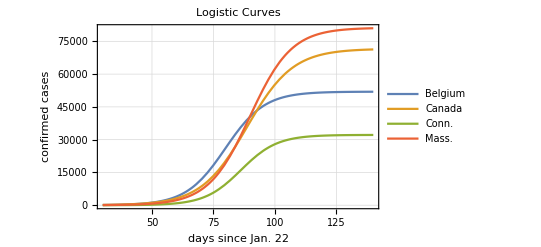

```mathematica
Plot[{logBelgium[t],logCanada[t],logConn[t],logMass[t]},{t,30,140},GridLines->Automatic,PlotRange->All,PlotLabel->Style["Logistic Curves",Bold,Black],PlotLegends->Placed[{"Belgium","Canada","Conn.","Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

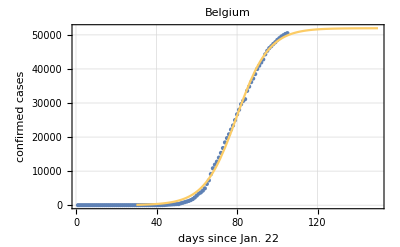

```mathematica
belt1=ListPlot[rawDataAll[[2;;,2]],PlotLegends->Placed[{"raw data"},{Left,Top}],PlotStyle->PointSize[Medium]];
belt2 =Plot[logBelgium[t],{t,30,150},PlotStyle->RGBColor[0.99,0.8,.4],PlotLegends->Placed[{"logistic fit"},{Left,Top}]];
Show[belt1,belt2,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Belgium",Bold,Black]]
```

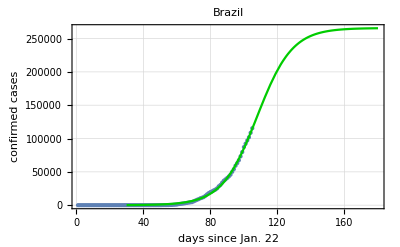

```mathematica
braz1=ListPlot[rawDataAll[[2;;,5]],PlotLegends->Placed[{"raw data"},{Left,Top}],PlotStyle->PointSize[Medium]];
braz2 =Plot[logBrazil[t],{t,30,180},PlotStyle->RGBColor[0,0.8,0],PlotLegends->Placed[{"logistic fit"},{Left,Top}]];
Show[braz1,braz2,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Brazil",Bold,Black]]
```

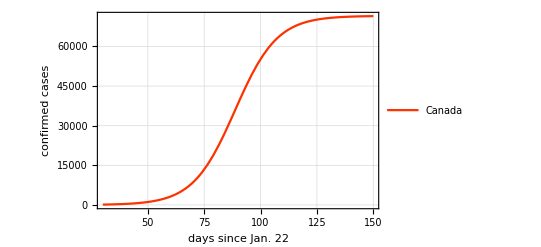

```mathematica
l3 = Plot[logCanada[t],{t,30,150},PlotStyle->RGBColor[.99,.20,0],GridLines->Automatic,PlotLegends->Placed[{"Canada"},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

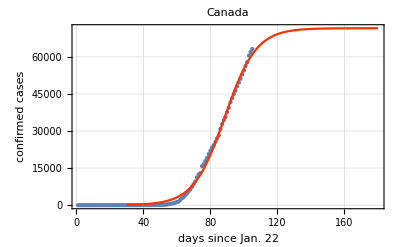

```mathematica
can1=ListPlot[rawDataAll[[2;;,8]],PlotLegends->Placed[{"raw data"},{Left,Top}],PlotStyle->PointSize[Medium]];
can2 =Plot[logCanada[t],{t,30,180},PlotStyle->RGBColor[0.99,0.2,0],PlotLegends->Placed[{"logistic fit"},{Left,Top}]];
Show[can1,can2,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Canada",Bold,Black]]
```

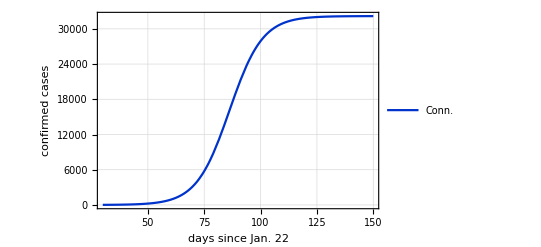

```mathematica
l4= Plot[logConn[t],{t,30,150},PlotStyle->RGBColor[0,.2,.8],GridLines->Automatic,PlotLegends->Placed[{"Conn."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

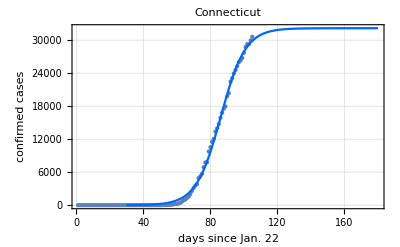

```mathematica
conn1=ListPlot[rawDataAll[[2;;,14]],PlotLegends->Placed[{"raw data"},{Left,Top}],PlotStyle->PointSize[Medium]];
conn2 =Plot[logConn[t],{t,30,180},PlotStyle->RGBColor[0,0.4,0.99],PlotLegends->Placed[{"logistic fit"},{Left,Top}]];
Show[conn1,conn2,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Connecticut",Bold,Black]]
```

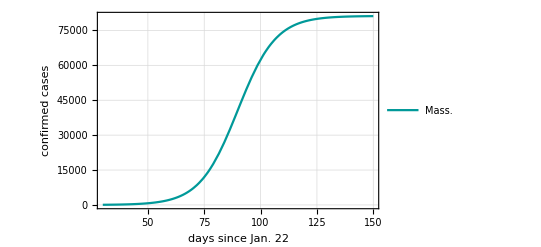

```mathematica
l5 = Plot[logMass[t],{t,30,150},PlotStyle->RGBColor[0,.6,.6],GridLines->Automatic,PlotLegends->Placed[{"Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"}]
```

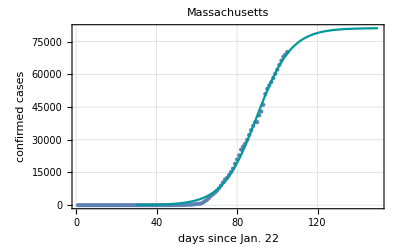

```mathematica
mass1=ListPlot[rawDataAll[[2;;,17]],PlotLegends->Placed[{"raw data"},{Left,Top}],PlotStyle->PointSize[Medium]];
mass2 =Plot[logMass[t],{t,30,150},PlotStyle->RGBColor[0,0.6,.6],PlotLegends->Placed[{"logistic fit"},{Left,Top}]];
Show[mass1,mass2,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Massachusetts",Bold,Black]]
```

```mathematica
logMass["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
L | 81210.7 | 1274.07 | 63.7413 | 5.49967×10^-84
k | 0.118297 | 0.00232143 | 50.9588 | 2.25791×10^-74
t0 | 89.8402 | 0.34225 | 262.498 | 3.56292×10^-146

### Gaussian

```mathematica
gaussBelgium=NonlinearModelFit[rawDataAll[[2;;,4]],gaussian2,{{A,1500},{μ,79},{σ,14}},t];
gbe=gaussBelgium["ParameterTableEntries"];
gaussBrazil=NonlinearModelFit[rawDataAll[[2;;,7]],gaussian2,{{A,50000},{μ,200},{σ,50}},t,MaxIterations->10000];
gbr=gaussBrazil["ParameterTableEntries"];
gaussCanada=NonlinearModelFit[rawDataAll[[2;;,10]],gaussian2,{{A,1673},{μ,85},{σ,15}},t];
gca=gaussCanada["ParameterTableEntries"];
gaussConn=NonlinearModelFit[rawDataAll[[2;;,16]],gaussian2,{{A,1023},{μ,86},{σ,13}},t];
gct=gaussConn["ParameterTableEntries"];
gaussMass=NonlinearModelFit[rawDataAll[[2;;,19]],gaussian2,{{A,925},{μ,83},{σ,13}},t];
gma=gaussMass["ParameterTableEntries"]
```

{{2243.27,105.278,21.3081,2.38775×10^-39},{91.1047,1.18964,76.5815,5.97475×10^-92},{15.3355,1.26945,12.0804,2.16804×10^-21}}

```mathematica
Grid[{{"Gaussian Parameters",SpanFromLeft},{"Place","A","μ","σ"},{"Belgium",gbe[[1]][[1]],gbe[[2]][[1]],gbe[[3]][[1]]},{"Brazil",gbr[[1]][[1]],gbr[[2]][[1]],gbr[[3]][[1]]},{"Canada",gca[[1]][[1]],gca[[2]][[1]],gca[[3]][[1]]},{"Conn.",gct[[1]][[1]],gct[[2]][[1]],gct[[3]][[1]]},{"Mass.",gma[[1]][[1]],gma[[2]][[1]],gma[[3]][[1]]}},Frame->All]
```

Gaussian Parameters |  |  | 
Place | A | μ | σ
Belgium | 1506.66 | 79.9991 | 14.1203
Brazil | 11649.8 | 132.605 | 26.2754
Canada | 1805.54 | 92.8629 | 19.2289
Conn. | 1008.3 | 87.0709 | 13.4477
Mass. | 2243.27 | 91.1047 | 15.3355

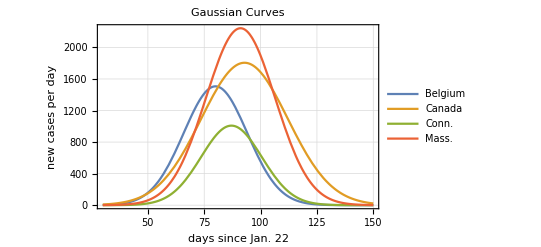

```mathematica
Plot[{gaussBelgium[t],gaussCanada[t],gaussConn[t],gaussMass[t]},{t,30,150},PlotRange->All,GridLines->Automatic,PlotRange->All,PlotLabel->Style["Gaussian Curves",Bold,Black],PlotLegends->Placed[{"Belgium","Canada","Conn.","Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","new cases per day"}]
```

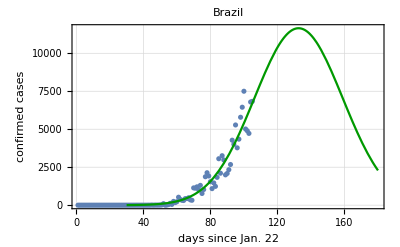

```mathematica
brg1=ListPlot[rawDataAll[[2;;,7]],PlotLegends->Placed[{"raw data"},{Left,Top}]];
brg2 =Plot[gaussBrazil[t],{t,30,180},PlotStyle->RGBColor[0,0.6,0],PlotLegends->Placed[{"gaussian fit"},{Left,Top}]];
Show[brg1,brg2,GridLines->Automatic,PlotRange->Full,Frame->True,FrameLabel->{"days since Jan. 22","confirmed cases"},PlotLabel->Style["Brazil",Bold,Black]]
```

### Derivative of logistic

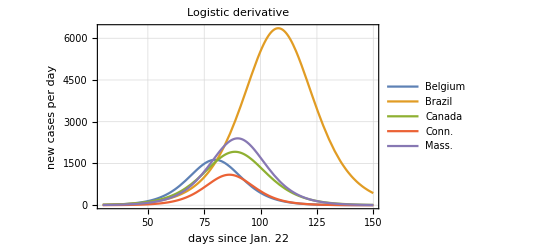

```mathematica
Plot[{logBelgium'[t],logBrazil'[t],logCanada'[t],logConn'[t],logMass'[t]},{t,30,150},GridLines->Automatic,PlotRange->All,PlotLabel->Style["Logistic derivative",Bold,Black],PlotLegends->Placed[{"Belgium","Brazil","Canada","Conn.","Mass."},{Left,Top}],Frame->True,FrameLabel->{"days since Jan. 22","new cases per day"}]
```